# CRNSSA Runtime Testing

```mathematica
<<CRNSSA`
```

## Direct SSA

All system constructions have number of reactions = number of species.

```mathematica
(*System 1: Every species appears in precisely 1 reaction. Every reaction has only 1 reactant and 1 product.*)
ConstructSys1[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[x[i],y[i],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 2: Every species appears in O(sqrt(n)) reactions. Every reaction has O(sqrt(n)) reactants and O(sqrt(n)) products.*)
ConstructSys2[n_]:=Module[
{k,rxns,xConcs,yConcs,concs},
k=Round[Sqrt[n]];
rxns= Flatten[Table[revrxn[Plus@@Table[x[i,l]+x[j,l],{l,k}],Plus@@Table[y[i,l]+y[j,l],{l,k}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]];
xConcs=Flatten[Table[conc[x[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
yConcs=Flatten[Table[conc[y[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 3: Every species appears in all reactions. Every reaction has O(n) reactants and O(n) products.*)
ConstructSys3[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[Plus@@Table[x[j],{j,n}],Plus@@Table[y[j],{j,n}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
TestSysSSA[construction_,algo_,kRange_,iters_,statesOnlyFlag_]:=Module[{},
Table[Module[
{n,rxns,concs,rxnsys,nRxns,nSpecies,results,totalTime,runtimeInfo,totalTimePerIter,algoTimePerIter,out},
n=k^2;
{rxns,concs} = construction[n];
rxnsys=Flatten[{rxns,concs}];
nRxns=Length[ExpandRevrxns[rxns]];
nSpecies=Length[SpeciesInRxnsys[rxnsys]];
results=Timing[SimulateDirectSSA[rxnsys,useIter->True,iterEnd->iters,statesOnly->statesOnlyFlag,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
totalTimePerIter=totalTime/iters;
runtimeInfo=GetRuntimeInfo[];
algoTimePerIter=runtimeInfo[[-1]][[-1]]/iters;
out={construction,statesOnlyFlag,nRxns,nSpecies,iters,totalTime,runtimeInfo,totalTimePerIter,algoTimePerIter};
Print[out];
out],
{k,kRange}]]
```

```mathematica
constructions={ConstructSys1,ConstructSys2,ConstructSys3};
algo="Opt";
kRange={1,3,5};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA=Table[TestSysSSA[constructions[[i]],algo,kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.171875,{{0.,0.},{0.,0.,0.,0.},{0.,0.171875,0.},{0.0000103,0.176903}},1.71875×10^-6,1.76903×10^-6}

{ConstructSys1,False,18,18,100000,0.265625,{{0.,0.},{0.,0.,0.,0.},{0.,0.265625,0.},{0.0000221,0.267042}},2.65625×10^-6,2.67042×10^-6}

{ConstructSys1,False,50,50,100000,0.5625,{{0.015625,0.},{0.,0.,0.,0.},{0.,0.546875,0.},{0.0000503,0.544384}},5.625×10^-6,5.44384×10^-6}

{ConstructSys1,True,2,2,100000,0.234375,{{0.,0.},{0.,0.,0.,0.},{0.,0.234375,0.},{3.5×10^-6,0.227565}},2.34375×10^-6,2.27565×10^-6}

{ConstructSys1,True,18,18,100000,0.28125,{{0.,0.},{0.,0.,0.,0.},{0.,0.28125,0.},{0.0000203,0.284496}},2.8125×10^-6,2.84496×10^-6}

{ConstructSys1,True,50,50,100000,0.65625,{{0.015625,0.},{0.,0.,0.,0.},{0.,0.640625,0.},{0.0000387,0.644748}},6.5625×10^-6,6.44748×10^-6}

{ConstructSys2,False,2,2,100000,0.1875,{{0.,0.},{0.,0.,0.,0.},{0.,0.171875,0.},{0.0000163,0.186764}},1.875×10^-6,1.86764×10^-6}

{ConstructSys2,False,18,18,100000,1.54688,{{0.,0.},{0.,0.,0.,0.},{0.,1.54688,0.},{0.0000348,1.5491}},0.0000154688,0.000015491}

{ConstructSys2,False,50,50,100000,5.84375,{{0.,0.},{0.,0.015625,0.015625,0.},{0.,5.8125,0.},{0.0001872,5.85365}},0.0000584375,0.0000585365}

{ConstructSys2,True,2,2,100000,0.140625,{{0.,0.},{0.,0.,0.,0.},{0.,0.140625,0.},{4.5×10^-6,0.143126}},1.40625×10^-6,1.43126×10^-6}

{ConstructSys2,True,18,18,100000,1.6875,{{0.,0.},{0.,0.,0.,0.},{0.,1.6875,0.},{0.0000325,1.68052}},0.000016875,0.0000168052}

{ConstructSys2,True,50,50,100000,5.65625,{{0.,0.},{0.,0.015625,0.015625,0.},{0.,5.625,0.},{0.000111,5.63563}},0.0000565625,0.0000563563}

{ConstructSys3,False,2,2,100000,0.140625,{{0.,0.},{0.,0.,0.,0.},{0.,0.140625,0.},{3.7×10^-6,0.151371}},1.40625×10^-6,1.51371×10^-6}

{ConstructSys3,False,18,18,100000,5.54688,{{0.015625,0.},{0.,0.,0.,0.},{0.,5.53125,0.},{0.0000401,5.54665}},0.0000554688,0.0000554665}

{ConstructSys3,False,50,50,100000,52.7969,{{0.,0.},{0.,0.03125,0.03125,0.},{0.,52.7344,0.},{0.000159,54.3806}},0.000527969,0.000543806}

{ConstructSys3,True,2,2,100000,0.15625,{{0.,0.},{0.,0.,0.,0.},{0.,0.15625,0.},{4.×10^-6,0.150129}},1.5625×10^-6,1.50129×10^-6}

{ConstructSys3,True,18,18,100000,5.95313,{{0.,0.},{0.,0.,0.,0.},{0.,5.95313,0.},{0.00004,5.97535}},0.0000595313,0.0000597535}

{ConstructSys3,True,50,50,100000,55.9219,{{0.015625,0.},{0.,0.015625,0.03125,0.},{0.,55.8594,0.},{0.0002411,57.2404}},0.000559219,0.000572404}

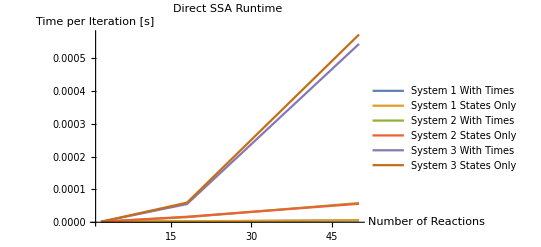

```mathematica
coorsSSA=Flatten[Table[
Table[{resultsSSA[[i]][[j]][[l]][[3]],resultsSSA[[i]][[j]][[l]][[9]]},{l,Length[resultsSSA[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2","System 3"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
(*coorsSSATotal=Flatten[Table[
Table[{resultsSSA[[i]][[j]][[l]][[3]],resultsSSA[[i]][[j]][[l]][[8]]},{l,Length[resultsSSA[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
coorsSSAAlgo=Flatten[Table[
Table[{resultsSSA[[i]][[j]][[l]][[3]],resultsSSA[[i]][[j]][[l]][[9]]},{l,Length[resultsSSA[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
coorsSSA=Flatten[{coorsSSATotal,coorsSSAAlgo},1]
constructionLabels={"System 1","System 2","System 3"};
statesOnlyLabels={" With Times"," States Only"};
timeLabels={" Total Runtime"," Backend Runtime"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]]<>timeLabels[[k]],{k,Length[timeLabels]},{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Optimized Direct SSA Runtime",
PlotRange->All]*)
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem], resultsSSA];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem], coorsSSA];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.171875,{{0.,0.},{0.,0.,0.,0.},{0.,0.171875,0.},{0.0000103,0.176903}},1.71875×10^-6,1.76903×10^-6},{ConstructSys1,False,18,18,100000,0.265625,{{0.,0.},{0.,0.,0.,0.},{0.,0.265625,0.},{0.0000221,0.267042}},2.65625×10^-6,2.67042×10^-6},{ConstructSys1,False,50,50,100000,0.5625,{{0.015625,0.},{0.,0.,0.,0.},{0.,0.546875,0.},{0.0000503,0.544384}},5.625×10^-6,5.44384×10^-6}},{{ConstructSys1,True,2,2,100000,0.234375,{{0.,0.},{0.,0.,0.,0.},{0.,0.234375,0.},{3.5×10^-6,0.227565}},2.34375×10^-6,2.27565×10^-6},{ConstructSys1,True,18,18,100000,0.28125,{{0.,0.},{0.,0.,0.,0.},{0.,0.28125,0.},{0.0000203,0.284496}},2.8125×10^-6,2.84496×10^-6},{ConstructSys1,True,50,50,100000,0.65625,{{0.015625,0.},{0.,0.,0.,0.},{0.,0.640625,0.},{0.0000387,0.644748}},6.5625×10^-6,6.44748×10^-6}}},{{{ConstructSys2,False,2,2,100000,0.1875,{{0.,0.},{0.,0.,0.,0.},{0.,0.171875,0.},{0.0000163,0.186764}},1.875×10^-6,1.86764×10^-6},{ConstructSys2,False,18,18,100000,1.54688,{{0.,0.},{0.,0.,0.,0.},{0.,1.54688,0.},{0.0000348,1.5491}},0.0000154688,0.000015491},{ConstructSys2,False,50,50,100000,5.84375,{{0.,0.},{0.,0.015625,0.015625,0.},{0.,5.8125,0.},{0.0001872,5.85365}},0.0000584375,0.0000585365}},{{ConstructSys2,True,2,2,100000,0.140625,{{0.,0.},{0.,0.,0.,0.},{0.,0.140625,0.},{4.5×10^-6,0.143126}},1.40625×10^-6,1.43126×10^-6},{ConstructSys2,True,18,18,100000,1.6875,{{0.,0.},{0.,0.,0.,0.},{0.,1.6875,0.},{0.0000325,1.68052}},0.000016875,0.0000168052},{ConstructSys2,True,50,50,100000,5.65625,{{0.,0.},{0.,0.015625,0.015625,0.},{0.,5.625,0.},{0.000111,5.63563}},0.0000565625,0.0000563563}}},{{{ConstructSys3,False,2,2,100000,0.140625,{{0.,0.},{0.,0.,0.,0.},{0.,0.140625,0.},{3.7×10^-6,0.151371}},1.40625×10^-6,1.51371×10^-6},{ConstructSys3,False,18,18,100000,5.54688,{{0.015625,0.},{0.,0.,0.,0.},{0.,5.53125,0.},{0.0000401,5.54665}},0.0000554688,0.0000554665},{ConstructSys3,False,50,50,100000,52.7969,{{0.,0.},{0.,0.03125,0.03125,0.},{0.,52.7344,0.},{0.000159,54.3806}},0.000527969,0.000543806}},{{ConstructSys3,True,2,2,100000,0.15625,{{0.,0.},{0.,0.,0.,0.},{0.,0.15625,0.},{4.×10^-6,0.150129}},1.5625×10^-6,1.50129×10^-6},{ConstructSys3,True,18,18,100000,5.95313,{{0.,0.},{0.,0.,0.,0.},{0.,5.95313,0.},{0.00004,5.97535}},0.0000595313,0.0000597535},{ConstructSys3,True,50,50,100000,55.9219,{{0.015625,0.},{0.,0.015625,0.03125,0.},{0.,55.8594,0.},{0.0002411,57.2404}},0.000559219,0.000572404}}}}

{{{2,1.76903×10^-6},{18,2.67042×10^-6},{50,5.44384×10^-6}},{{2,2.27565×10^-6},{18,2.84496×10^-6},{50,6.44748×10^-6}},{{2,1.86764×10^-6},{18,0.000015491},{50,0.0000585365}},{{2,1.43126×10^-6},{18,0.0000168052},{50,0.0000563563}},{{2,1.51371×10^-6},{18,0.0000554665},{50,0.000543806}},{{2,1.50129×10^-6},{18,0.0000597535},{50,0.000572404}}}

## Bounded Tau Leaping

```mathematica
<<CRNSSA`
```

```mathematica
ConstructSysBTL[n_]:={
rxnl[{x1,x2},{y},1],
conc[x1,n/2-1],
conc[x2,n/2+1]
};
```

```mathematica
TestSysBTL[construction_,simulation_,nRange_]:=Module[{},
Table[Module[
{rxnsys,results,totalTime,runtimeInfo,algoTime},
rxnsys= construction[n];
results=Timing[simulation[rxnsys,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
runtimeInfo=GetRuntimeInfo[];
algoTime=runtimeInfo[[-1]][[-1]];
out={simulation,n,totalTime,runtimeInfo,algoTime};
Print[out];
out],
{n,nRange}]]
```

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[10^i,{i,1,3}];
resultsBTL=Table[TestSysBTL[ConstructSysBTL,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,10,0.,{{0.,0.},{0.,0.,0.,0.},{0.,0.,0.},{4.8×10^-6,0.0000307}},0.0000307}

{SimulateDirectSSA,100,0.,{{0.,0.},{0.,0.,0.,0.},{0.,0.,0.},{1.9×10^-6,0.0000779}},0.0000779}

{SimulateDirectSSA,1000,0.,{{0.,0.},{0.,0.,0.,0.},{0.,0.,0.},{3.3×10^-6,0.0005852}},0.0005852}

{SimulateBoundedTauLeaping,10,0.,{{2.3×10^-6,0.000017}},0.000017}

{SimulateBoundedTauLeaping,100,0.015625,{{2.7×10^-6,0.0001207}},0.0001207}

{SimulateBoundedTauLeaping,1000,0.,{{1.9×10^-6,0.0003682}},0.0003682}

{{{10,0.0000307},{100,0.0000779},{1000,0.0005852}},{{10,0.000017},{100,0.0001207},{1000,0.0003682}}}

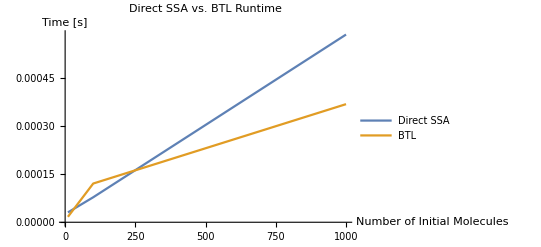

```mathematica
coorsBTL=Table[
Table[{resultsBTL[[i]][[l]][[2]],resultsBTL[[i]][[l]][[5]]},{l,Length[resultsBTL[[i]]]}],
{i,Length[simulations]}]
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem], resultsBTL];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem], coorsBTL];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,10,0.,{{0.,0.},{0.,0.,0.,0.},{0.,0.,0.},{4.8×10^-6,0.0000307}},0.0000307},{SimulateDirectSSA,100,0.,{{0.,0.},{0.,0.,0.,0.},{0.,0.,0.},{1.9×10^-6,0.0000779}},0.0000779},{SimulateDirectSSA,1000,0.,{{0.,0.},{0.,0.,0.,0.},{0.,0.,0.},{3.3×10^-6,0.0005852}},0.0005852}},{{SimulateBoundedTauLeaping,10,0.,{{2.3×10^-6,0.000017}},0.000017},{SimulateBoundedTauLeaping,100,0.015625,{{2.7×10^-6,0.0001207}},0.0001207},{SimulateBoundedTauLeaping,1000,0.,{{1.9×10^-6,0.0003682}},0.0003682}}}

{{{10,0.0000307},{100,0.0000779},{1000,0.0005852}},{{10,0.000017},{100,0.0001207},{1000,0.0003682}}}